### Parameter definitions

```mathematica
FullSimplify[1/(2 d^3)((4+3q)L[t]-(3q M^2 ξ)/(q+1) L[t]/Norm[L[t]]  + S2[t]   )   /.ξ->M^-2 Dot[((1+q)S1[t]+(1+q^-1)S2[t]),L[t]/Norm[L[t]]]/.L[t] ->J[t]-S1[t]-S2[t]]
FullSimplify[1/(2 d^3)((4+3/q)L[t]-(3 M^2 ξ)/(q+1) L[t]/Norm[L[t]]  + S1[t]    )    /.ξ->M^-2 Dot[((1+q)S1[t]+(1+q^-1)S2[t]),L[t]/Norm[L[t]]]/.L[t] ->J[t]-S1[t]-S2[t]]
```

1/2 (5.8 (J[t]-S1[t]-S2[t])-(0.18 (J[t]-S1[t]-S2[t]))/Norm[J[t]-S1[t]-S2[t]]+S2[t])

1/2 (S1[t]+9. (J[t]-S1[t]-S2[t])-(0.3 (J[t]-S1[t]-S2[t]))/Norm[J[t]-S1[t]-S2[t]])

```mathematica
d=1;
(*Use xi. Don't specify arbitrarity. Replace xi with L, S1, S2 vectors in NDSolve.

Think about how to take care of NDSolve.

Perform xcaptest. Should be constant
*)
q=0.6;
ξ=0.16;
M=1;
```

### Differential equations

```mathematica
dS1[t_] =   Cross[1/(2 d^3)((4+3q)(J[t]-S1[t]-S2[t])-(3q M^2 ξ)/(q+1) (J[t]-S1[t]-S2[t])/Norm[J[t]-S1[t]-S2[t]]  + S2[t]   ),S1[t]];
dS2[t_] =    Cross[1/(2 d^3)((4+3/q)(J[t]-S1[t]-S2[t])-(3 M^2 ξ)/(q+1) (J[t]-S1[t]-S2[t])/Norm[J[t]-S1[t]-S2[t]]  + S1[t]    ) ,S2[t]];
dJ[t_]=     {0,0,0}  ;
```

### Numerical solution

```mathematica
sol=NDSolve[{S1'[t]== dS1[t]   , S2'[t]==dS2[t] , J'[t]==dJ[t],S1[0]=={-3,-6,-1},S2[0]=={-4,-6,-3}, J[0]=={0,0,10}   },   {S1,S2,J},{t,0,30}];
```

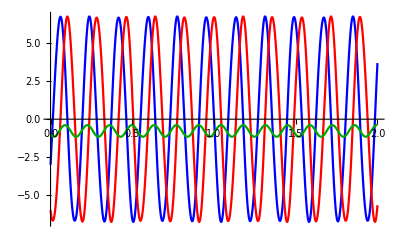

```mathematica
output[t_]:= (S1/.sol[[1]])[t];
Plot[{output[t][[1]],output[t][[2]],output[t][[3]]}, {t,0,2},PlotStyle->{Blue,Red,Darker[Green]}]
```

#### Vector definitions with numerical solution

```mathematica
S1v[t_]:=(S1/.sol[[1]])[t];
S2v[t_]:=(S2/.sol[[1]])[t];
Jv[t_]:=(J/.sol[[1]])[t];
Lv[t_]:=Jv[t]-S1v[t]-S2v[t];
Sv[t_]:=S1v[t]+S2v[t];
```

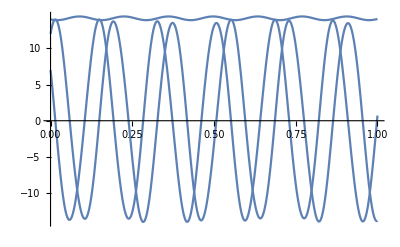

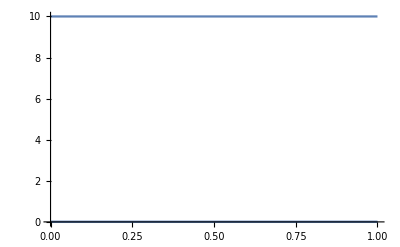

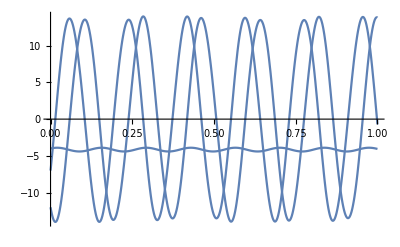

```mathematica
Plot[Lv[t],{t,0,1}]
Plot[Jv[t],{t,0,1}]
Plot[Sv[t],{t,0,1}]
```

#### Vector modulus

```mathematica
NormS1[t_]:=Norm[S1v[t]];
NormS2[t_]:=Norm[S2v[t]];
NormJ[t_]:=Norm[Jv[t]];
NormL[t_]:=Norm[Lv[t]];
NormS[t_]:=Norm[Sv[t]];
```

#### Unit vector definitions

```mathematica
S1u[t_]:=S1v[t]/NormS1[t];
Su[t_]:=Sv[t]/NormS[t];
```

#### Cartesian unit vectors

```mathematica
zcap[t_]:={0,0,1}
```

```mathematica
xcap[t_]:={1,0,0}
```

```mathematica
ycap[t_]:=Cross[zcap[t],xcap[t]]
```

#### Cartesian unit vectors test

```mathematica
Simplify[Simplify[Solve[{Jvec == Jz zcap, Lvec == Lx xcap + Ly ycap + Lz zcap , Svec == Sx xcap + Sy ycap + Sz zcap  } , {xcap, ycap, zcap}]]/.{Jx->0,Jy->0}]
```

{{xcap→(Jz Ly Svec-Jz Lvec Sy+Jvec Lz Sy-Jvec Ly Sz)/(Jz Ly Sx-Jz Lx Sy),ycap→-(Jz Lx Svec-Jz Lvec Sx+Jvec Lz Sx-Jvec Lx Sz)/(Jz Ly Sx-Jz Lx Sy),zcap→Jvec/Jz}}

```mathematica
numX[t_]:=Jv[t][[3]] Lv[t][[2]]Sv[t]-Jv[t][[2]] Lv[t][[3]]Sv[t]-Jv[t][[3]] Lv[t]Sv[t][[2]]+Jv[t] Lv[t][[3]]Sv[t][[2]]+Jv[t][[2]] Lv[t]Sv[t][[3]]-Jv[t] Lv[t][[2]] Sv[t][[3]];

denX[t_]:=Jv[t][[3]] Lv[t][[2]]Sv[t][[1]]-Jv[t][[2]] Lv[t][[3]]Sv[t][[1]]-Jv[t][[3]] Lv[t][[1]]Sv[t][[2]]+Jv[t][[1]] Lv[t][[3]]Sv[t][[2]]+Jv[t][[2]] Lv[t][[1]]Sv[t][[3]]-Jv[t][[1]] Lv[t][[2]]Sv[t][[3]];
```

```mathematica
numX1[t_]:=Jv[t][[3]] Lv[t][[2]]Sv[t]-Jv[t][[3]] Lv[t]Sv[t][[2]]+Jv[t] Lv[t][[3]]Sv[t][[2]]-Jv[t] Lv[t][[2]] Sv[t][[3]];
denX1[t_]:=Jv[t][[3]] Lv[t][[2]]Sv[t][[1]]-Jv[t][[3]] Lv[t][[1]]Sv[t][[2]];
```

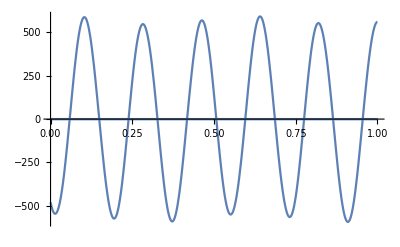

```mathematica
Plot[Jv[t][[3]] Lv[t][[2]]Sv[t]-Jv[t][[3]] Lv[t]Sv[t][[2]]+Jv[t] Lv[t][[3]]Sv[t][[2]],{t,0,1},PlotRange->All]
```

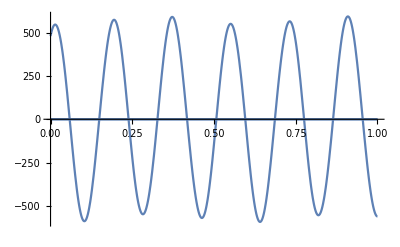

```mathematica
Plot[-Jv[t] Lv[t][[2]] Sv[t][[3]],{t,0,1}]
```

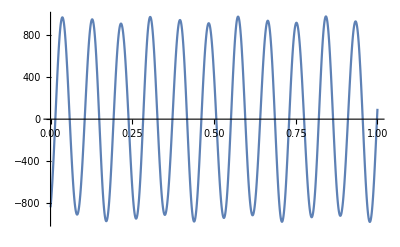

```mathematica
Plot[Jv[t][[3]] Lv[t][[2]]Sv[t][[1]],{t,0,1}]
```

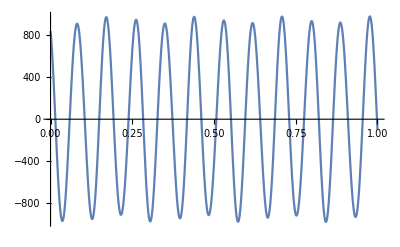

```mathematica
Plot[-Jv[t][[3]] Lv[t][[1]]Sv[t][[2]],{t,0,1}]
```

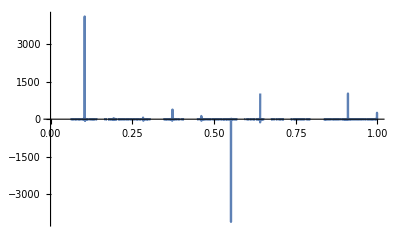

```mathematica
xcapTest[t_]:=numX1[t]/denX1[t] ;
Plot[xcapTest[t],{t,0,1}]
```

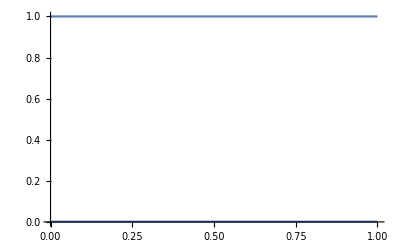

```mathematica
zcapZ[t_]:=Jv[t]/(Jv[t][[3]])
Plot[zcapZ[t],{t,0,1}]
```

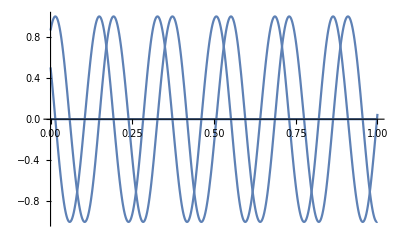

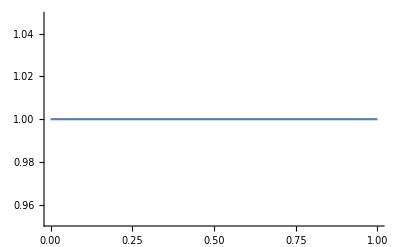

```mathematica
xcapX[t_]:=(Lv[t]-(Dot[Lv[t],zcapZ[t]]zcapZ[t]))/Norm[Lv[t]-(Dot[Lv[t],zcapZ[t]]zcapZ[t])]
Plot[xcapX[t],{t,0,1}]
Plot[Norm[xcapX[t]],{t,0,1}]
```

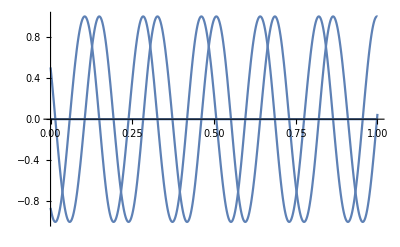

-Graphics-

```mathematica
ycapY[t_]:=Cross[zcapZ[t],xcapX[t]]
Plot[ycapY[t],{t,0,1}]
Plot[Norm[ycapY[t]],{t,0,1}]
```

#### Orthogonal vector definition

```mathematica
SO1[t_]:=Cross[ycapY[t],Sv[t]];
NormSO[t_]:=Norm[SO1[t]];
SOu[t_]:=SO1[t]/NormSO[t]
```

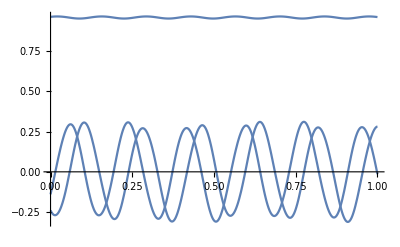

```mathematica
Plot[SOu[t],{t,0,1},PlotRange->All]
```

#### Angle ϕ' definitions

```mathematica
cosϕ1[t_]:=Dot[S1u[t],SOu[t]]/Norm[Cross[S1u[t],Su[t]]];
```

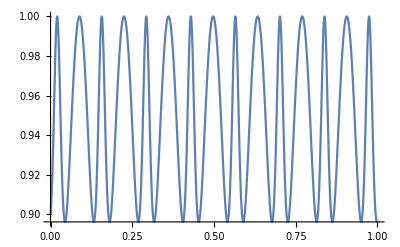

```mathematica
Plot[cosϕ1[t],{t,0,1},PlotRange->All]
```